Angle of Repose
Shiva Shahrokhi and Aaron T. Becker
when granular media is dropped in a pile, it forms a cone.  The maximum slope of the cone depends on the material used, but is very repeatable (due to CLT) and is called the angle of repose.  
Robot swarms, such as the Kilobot, also have an angle of repose.

https://en.wikipedia.org/wiki/Angle_of_repose
The angle of repose, or critical angle of repose,[1] of a granular material is the steepest angle of descent or dip relative to the horizontal plane to which a material can be piled without slumping. At this angle, the material on the slope face is on the verge of sliding. The angle of repose can range from 0° to 90°.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## A manipulate environment for angle of repose

```mathematica
l = 1; (*width of bar holding material*)
Manipulate[Module[{a,b,p,c,lside,h,d,Area},
Graphics[ {
a= l/2*{Cos[θ],Sin[θ]};
b = l/2*{Cos[α],Sin[α]};
c = l/2*{1,0};
p =  l/10*{Sin[θ],-Cos[θ]};
h = l/2;
d = l/2;

White,Rectangle[{-l,-l},{l,2}],

Pink,(*Rotate[Rectangle[{-l/2,-.1},{l/2,0}],-θ π/180,{0,0}]}],*)
Polygon[{a,a+p,-a+p,-a}],
(* draw piles of stuff on ground*)
Brown,Polygon[{{-l/2Cos[θ]-h Cos[α],-d-h},{-l/2Cos[θ],h Sin[α]-h-d},{-l/2Cos[θ]+h Cos[α],-h-d}}],
Brown,Polygon[{{l/2Cos[θ]-h Cos[α],-d-h},{l/2Cos[θ],h Sin[α]-h-d},{l/2Cos[θ]+h Cos[α],-h-d}}],
(*granular media*)
If[α>Abs[θ],
{lside=(l Sin[θ+α])/Sin[π-2α];Polygon[{a,lside{Cos[α],Sin[α]}-a,-a}]},lside=0;],
(*Black,Text[N[{l/2Cos[θ]+h Cos[α],-h-d}],{0,0}],*)

(*draw angle of repose*)
Black,Line[{-a+c/2,-a,-a+ l/4*{Cos[α],Sin[α]}}],
Black,Line[{a-c/2,a,a+ l/4*{-Cos[α],Sin[α]}}],
Circle[-a,l/6,{0,α}],
Circle[a,l/6,{π,π-α}],
(* measure weight of granular media  (proportional to area of triangle)*)
Area = 1/2 lside l Sin[α-θ];
Black,Text[StringForm["Area = ``",N[Round[Area,0.01]]],{0,-1/2}],

(*measure torque of granular media*)
(*draw a scale*)
Blue,PointSize[Large],Point[{0,0}]


}]],
{{α,π/4,"Angle of Repose"} ,0,5π/12,π/36,Appearance->"Labeled"},
{{θ,0} ,- 5π/12, 5π/12,π/36,Appearance->"Labeled"},
(*add setter bar so you can select the material to use.  Should change the angle or repose and the color of the granular media*)
{material,{"sand","salt","corn","wheat"}}
]
```

## Compute the Torque about the center of the object (manipulate trials)

```mathematica
heightBottom[x_,θ_]:=Tan[θ]x;
heightTop[x_,α_,l_,θ_] := Min[  Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ]), -Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])]; 
(*Torque[θ_,α_,l_] := ∫_(-l/2Cos[θ])^(l/2Cos[θ]) x(heightTop[x,α,l,θ]-heightBottom[x,θ])ⅆx*)
Torque1[θ_,α_,l_] := ∫_(-l/2Cos[θ])^(l/2Cos[θ]) x(heightTop[x,α,l,θ]-heightBottom[x,θ])ⅆx
```

Angle of repose for  a list of materials :
  Ashes 40
Asphalt 30
Bark

```mathematica
FullSimplify[x(heightTop[x,α,l,θ]-heightBottom[x,θ])]
```

x (Min[1/2 l Sec[α] Sin[α+θ]-x Tan[α],1/2 l Sec[α] Sin[α-θ]+x Tan[α]]-x Tan[θ])

```mathematica
1/2 Min[ Sec[α] (-2 x Sin[α]+Sin[α+θ]), (-Sin[θ]+(2 x+Cos[θ]) Tan[α])]-x Tan[θ]
```

1/2 Min[Sec[α] (-2 x Sin[α]+Sin[α+θ]),-Sin[θ]+(2 x+Cos[θ]) Tan[α]]-x Tan[θ]

```mathematica
Manipulate[Plot[{heightTop[x,α,1,θ],heightBottom[x,θ]},{x,-1,1}],{{α,π/4,"Angle of Repose"} ,0,5π/12,π/36,Appearance->"Labeled"},
{{θ,0} ,- 5π/12, 5π/12,π/36,Appearance->"Labeled"}]
```

```mathematica
Clear[l]
a= l/2*{Cos[θ],Sin[θ]};
lside=(l Sin[θ+α])/Sin[π-2α];FullSimplify[lside{Cos[α],Sin[α]}-a]
xMid = (*Cos[α](l Sin[θ+α])/Sin[π-2α]-l/2Cos[θ]*) (l Cot[α] Sin[θ])/2;
(*FullSimplify[ Cos[α](l Sin[θ+α])/Sin[π-2α]-l/2Cos[θ]] = (l Cot[α] Sin[θ])/2*)
```

{1/2 l Cot[α] Sin[θ],1/2 l Cos[θ] Tan[α]}

```mathematica
heightTop[x_,α_,l_,θ_] := Min[  Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ]), -Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])];
```

```mathematica
144/6
```

24

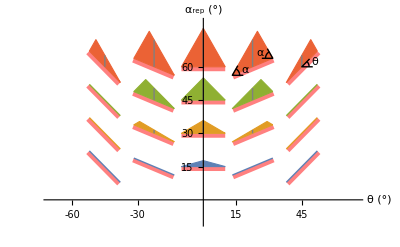
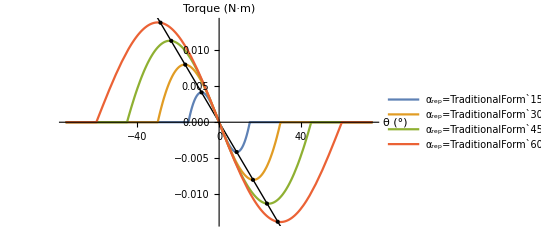
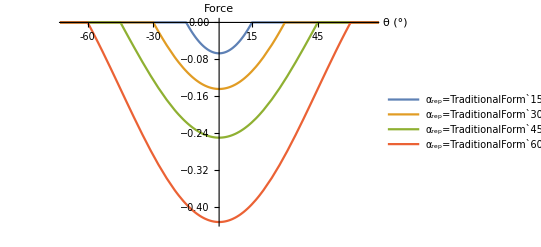
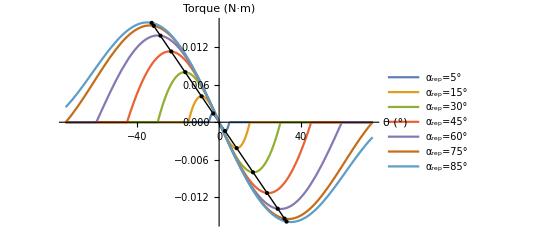
## Plot force and torque (figures for paper) -Graphics--Graphics--Graphics- Max torque curve as a function of theta does look linear (approximately -θ/36, but actual curve is -(l^3 (-1+6 θ^2+Cos[2 θ]) Sin[θ])/(144 θ^2)) (given a theta, find the angle of repose that maximizes it): -Graphics-

```mathematica
(*torque simplified*)FullSimplify[Assuming[Cos[θ]≥ Cos[α], ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) x(Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+ ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) x(-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]]
```

1/48 l^3 (-Cos[2 α]+Cos[2 θ]) Csc[α]^2 Sin[θ]

```mathematica
(*Force simplified*)
FullSimplify[Assuming[Cos[θ]≥ Cos[α]≥0, ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) (Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) (-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]]
```

1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α]

```mathematica
Maximizing torque  l^3(Cos[2α]-Cos[2θ])/(48 Sin[α]^2)Sin[θ], when θm = Sin[α]/(√3)
α = ArcSin[√3 θm ]
```

```mathematica
FullSimplify[ l^3(Cos[2α]-Cos[2 Sin[α]/(√3)])/(48 Sin[α]^2)Sin[Sin[α]/(√3)]]
```

1/48 l^3 (Cos[2 α]-Cos[(2 Sin[α])/(√3)]) Csc[α]^2 Sin[Sin[α]/(√3)]

```mathematica
FullSimplify[l^3(Cos[2ArcSin[√3 θ ]]-Cos[2θ])/(48 Sin[ArcSin[√3 θ ]]^2)Sin[θ]]
```

-(l^3 (-1+6 θ^2+Cos[2 θ]) Sin[θ])/(144 θ^2)

```mathematica
(*Do a linear fit at 0 *)
Limit[(-(l^3 (-1+6 θ^2+Cos[2 θ]) Sin[θ])/(144 θ^2))/θ,θ->0]
```

-l^3/36

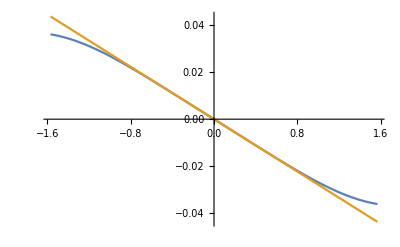

```mathematica
Plot [{-((-1+6 θ^2+Cos[2 θ]) Sin[θ])/(144 θ^2),-θ/36},{θ,-Pi/2, Pi/2}]
```

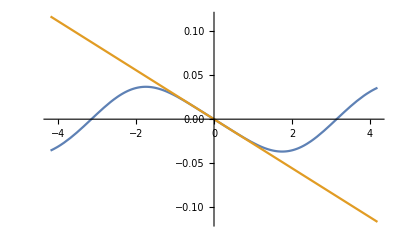

```mathematica
Plot [{-((-1+6 θ^2+Cos[2 θ]) Sin[θ])/(144 θ^2),-θ/36},{θ,-4Pi/3, 4Pi/3}]
```

#### Final equations :

```mathematica
Torque[θ_,α_,l_] :=If[Cos[θ]<Cos[α],0, ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) x(Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) x(-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]
(*  
  sec(z)==1/cos(z) 
csc(z)==1/sin(z).
 *)
(*torque equation evaluated*)
torqAOR[θ_,α_,l_]:=If[Abs[θ]<α, l^3(Cos[2α]-Cos[2θ])/(48 Sin[α]^2)Sin[θ],0]
Force[θ_,α_,l_] :=If[Cos[θ]<Cos[α],0, 
∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) (Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) (-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]
```

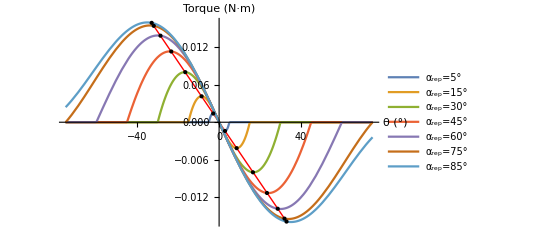

```mathematica
aDeg = {5,15,30,45,60,75,85};
aorP=Plot[Evaluate[Table[torqAOR[θ π/180,aDeg ⟦n⟧π/180,1],{n,1,Length[aDeg ]}]],{θ,-75,75},PlotRange->All,
PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Left,.2}],AxesLabel->{"θ (°)","Torque (N·m)"},

Prolog->Module[{θmax=(√(Sin[π/2]^2))/(√3)} ,{Thin,Red,Line[{{-θmax 180/π ,-torqAOR[θmax,π/2,1]},{θmax 180/π ,torqAOR[θmax,π/2,1]}
}]}],
Epilog->Module[{θmax} ,{Table[ θmax=(√(Sin[aDeg ⟦n⟧π/180]^2))/(√3);
{Point[{  θmax 180/π ,   torqAOR[θmax,aDeg ⟦n⟧π/180,1]}],
Point[{-θmax 180/π ,-torqAOR[θmax,aDeg ⟦n⟧π/180,1]}]
},{n,1,Length[aDeg ]}]}]]
(*Export["../pictures/pdf/AngleOfReposeTorque.pdf",%];*)
```

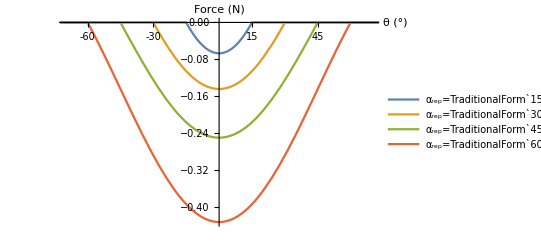

```mathematica
aDeg = {15,30,45,60};
as =aDeg π/180;
l=1;
SetDirectory[NotebookDirectory[]];
Plot[Evaluate[Table[-Force[θ π/180,a ,1],{a,as}]],{θ,-90,90},
Ticks->{{-60,-45,-30,-15,15,30,45,60},Automatic},PlotRange-> {{-70,70},Automatic},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Left,Bottom}],AxesLabel->{"θ (°)","Force (N)"}]
Export["../pictures/pdf/AngleOfReposeForce.pdf",%];
```

```mathematica
FullSimplify[If[Cos[θ]<Cos[α],0, ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) (Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) (-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]]
```

If[Cos[θ]<Cos[α],0,∫_(1/2 (-l) Cos[θ])^(1/2 l Cot[α] Sin[θ]) (Tan[α] x+1/2 l (Cos[θ] Tan[α]-Sin[θ])-Tan[θ] x)ⅆx+∫_(1/2 l Cot[α] Sin[θ])^(1/2 l Cos[θ]) (-Tan[α] x+1/2 l (Cos[θ] Tan[α]+Sin[θ])-Tan[θ] x)ⅆx]

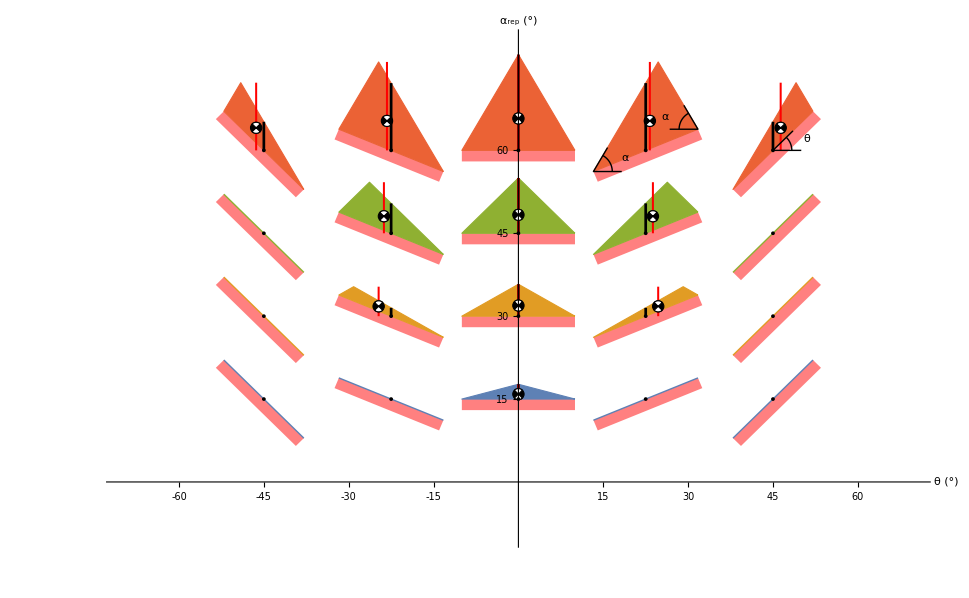

```mathematica
heightTop[x_,α_,l_,θ_] := Min[  Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ]), -Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])]; 
DrawGranular[θ_,α_,s_,colr_]:=Module[{a,p,h,d,lside,com},
l = 20; (*length*)
a= l/2*{Cos[θ],Sin[θ]};
p =  l/10*{Sin[θ],-Cos[θ]};
h = l/2;
d = l/2;
{Pink,Polygon[{s+a,s+a+p,s+-a+p,s-a}],EdgeForm[{colr}],colr,
(*granular media*)
If[α>Abs[θ],
{lside=(l Sin[θ+α])/Sin[π-2α];
com =1/3 (s+a+s+lside{Cos[α],Sin[α]}-a+s-a);
Polygon[{s+a,s+lside{Cos[α],Sin[α]}-a,s-a}],
Black,Thickness[0.002], Line[{s,s+{0,If[Abs[θ]>α,0,heightTop[0,α,l,θ]] }}]  (*draw line up the middle*),
{
(*draw the center-of-mass (COM *)
Thickness[0.0015],Red, (*Line[{s+{com⟦1⟧,0},s+{com⟦1⟧,heightTop[com⟦1⟧,α,l,θ]}}],*)
Line[{{com⟦1⟧,s⟦2⟧},{com⟦1⟧,s⟦2⟧ + 3(com⟦2⟧-s⟦2⟧)}}],
EdgeForm[Directive[Black,Thin]],Black,Disk[com,1], White,Disk[com,1,{45 Degree,135 Degree}],Disk[com,1,{-45 Degree,-135 Degree}]}
},Line[{s+a,s-a}]],
{Black,EdgeForm[None],Disk[s,1/3]}
}
]
aDeg = {15,30,45,60};
as =aDeg π/180;
l=1;
SetDirectory[NotebookDirectory[]];
Plot[{-50},{θ,-90,90},Ticks->{{-60,-45,-30,-15,15,30,45,60},aDeg},PlotRange-> {{-70,70},{-10,80}},AxesLabel->{"θ (°)","α_rep (°)"},Prolog->{
Table[DrawGranular[theta π/180,aDeg⟦i⟧ π/180,{theta,aDeg⟦i⟧},ColorData[97,"ColorList"]⟦i⟧],{i,Length[aDeg]},{theta,{-45,-22.5,0,22.5,45}}]
},
Epilog->
Module[{a,c,α=π/3,θ,l = 20,b},
{
θ=π/8;
c ={θ*180/π,α 180/π};
a= l/2*{Cos[θ],Sin[θ]};
b= l/4*{1,0};
Black,Line[{c-a+b,c-a,c-a+ l/4*{Cos[α],Sin[α]}}],
Black,Line[{c+a-b,c+a,c+a+ l/4*{-Cos[α],Sin[α]}}],
Circle[c-a,l/6,{0,α}],  (*draw a few alpha angles*)
Circle[c+a,l/6,{π,π-α}],
Text["α",c-{3.6,1.4}],Text["α",c+{3.5,6}],

θ=π/4;
c ={θ*180/π,α 180/π};
a= l/2*{Cos[θ],Sin[θ]};
b= l/4*{1,0};
Black,Line[{c+b,c,c+ l/4*{Cos[θ],Sin[θ]}}],
Circle[c,l/6,{0,θ}],
Text["θ",c+{6,2}]
}
]
] 
(*Export["../pictures/pdf/AngleOfRepose.pdf",%];*)
```

## Calculate mean and variance as a function of β,α, and ell

```mathematica
l= 1;
heightUpper[x_,α_,θ_] := Min[ (x+l/2) Tan[α+θ],-(x-l/2) Tan[α-θ]]
Manipulate[Module[{β},
If[θ≤ -α,θ=-α+0.001];
If[θ≥ α,θ=α-0.001];
β = θ-π/2;
Plot[heightUpper[x,α,θ],{x,-l/2,l/2},PlotRange->{{-l/2,l/2},l{-.1,.9}},AspectRatio->1,Filling->0,
Epilog->{Text["β",{l/16,l/2}],Arrow[{{0,l/2},{.2Cos[β],l/2+.2Sin[β]}}]
}
]],
{{α,π/4,"Angle of Repose"} ,0,π/2-π/36,π/36,Appearance->"Labeled"},
{{θ,0} ,- 5π/12, 5π/12,π/36,Appearance->"Labeled"}]
```

```mathematica
l= 1;
heightUpper[x_,α_,θ_] := Min[ (x+l/2) Tan[α+θ],-(x-l/2) Tan[α-θ]]
Manipulate[Module[{β,l1,peak,com},
If[θ≤ -α,θ=-α+0.001];
If[θ≥ α,θ=α-0.001];
β = θ-π/2;
l1 = -1/4 l Csc[α] Sec[α] Sin[2 θ];
com = {-1/6 l Cos[θ] Csc[α] Sec[α] Sin[θ],1/12 l (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α]};
Plot[heightUpper[x,α,θ],{x,-l/2,l/2},PlotRange->{{-l/2,l/2},l{-.1,.9}},AspectRatio->1,Filling->0,
Epilog->{Text["β",{l/32,l*0.52}],Arrow[{{0,l/2},{.2Cos[β],l/2+.2Sin[β]}}],
peak={l1,(l1+l/2) Tan[α+θ]};
Red,Line[{{l1,0},peak}],
Arrow[{peak,peak+{.2Cos[β],.2Sin[β]}}],
EdgeForm[Directive[Black,Thin]],Black,Disk[com,1/64], White,Disk[com,1/64,{45 Degree,135 Degree}],Disk[com,1/64,{-45 Degree,-135 Degree}]
}
]],
{{α,π/4,"Angle of Repose"} ,0,π/2-π/36,π/36,Appearance->"Labeled"},
{{θ,0} ,- 5π/12, 5π/12,π/36,Appearance->"Labeled"}]
```

Plot::plln: Limiting value -l/2 in {x,-l/2,l/2} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

```mathematica
(*solve for l1*)
Clear[l]
FullSimplify[l (Sin[α-θ]Cos[α+θ])/Sin[π-2α]-l/2]
```

-1/4 l Csc[α] Sec[α] Sin[2 θ]

## Calculate mean, variance, and covariance

```mathematica
Clear[l,θ,α]
```

```mathematica
(*area*)
FullSimplify[∫_(-l/2)^(-1/4 l Csc[α] Sec[α] Sin[2 θ]) (∫_0^((x+l/2) Tan[α+θ]) 1ⅆy)ⅆx +∫_(-1/4 l Csc[α] Sec[α] Sin[2 θ])^(l/2) (∫_0^(-(x-l/2) Tan[α-θ]) 1ⅆy)ⅆx]
```

1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α]

```mathematica
(*meanx*A*)
FullSimplify[∫_(-l/2)^(-1/4 l Csc[α] Sec[α] Sin[2 θ]) (∫_0^((x+l/2) Tan[α+θ]) xⅆy)ⅆx +∫_(-1/4 l Csc[α] Sec[α] Sin[2 θ])^(l/2) (∫_0^(-(x-l/2) Tan[α-θ]) xⅆy)ⅆx]
```

1/96 l^3 (Cos[2 α]-Cos[2 θ]) Csc[α]^2 Sec[α]^2 Sin[2 θ]

```mathematica
(*xmean*)
FullSimplify[(1/96 l^3 (Cos[2 α]-Cos[2 θ]) Csc[α]^2 Sec[α]^2 Sin[2 θ])/(1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])]
```

-1/6 l Cos[θ] Csc[α] Sec[α] Sin[θ]

```mathematica
(*ymean*A*)
FullSimplify[∫_(-l/2)^(-1/4 l Csc[α] Sec[α] Sin[2 θ]) (∫_0^((x+l/2) Tan[α+θ]) yⅆy)ⅆx +∫_(-1/4 l Csc[α] Sec[α] Sin[2 θ])^(l/2) (∫_0^(-(x-l/2) Tan[α-θ]) yⅆy)ⅆx]
```

1/96 l^3 (Cos[2 α]-Cos[2 θ])^2 Csc[α]^2 Sec[α]^2

```mathematica
(*ymean*)
FullSimplify[(1/96 l^3 (Cos[2 α]-Cos[2 θ])^2 Csc[α]^2 Sec[α]^2)/(1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])]
```

1/12 l (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α]

```mathematica
(*y var *A *)
FullSimplify[∫_(-l/2)^(-1/4 l Csc[α] Sec[α] Sin[2 θ]) (∫_0^((x+l/2) Tan[α+θ]) (y-1/12 l (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])^2 ⅆy)ⅆx +∫_(-1/4 l Csc[α] Sec[α] Sin[2 θ])^(l/2) (∫_0^(-(x-l/2) Tan[α-θ]) (y-1/12 l (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])^2 ⅆy)ⅆx]
```

-1/288 l^4 (Cot[2 α]-Cos[2 θ] Csc[2 α])^3

```mathematica
(*y var *)
FullSimplify[(-1/288 l^4 (Cot[2 α]-Cos[2 θ] Csc[2 α])^3)/(1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])]
```

1/72 l^2 (Cot[2 α]-Cos[2 θ] Csc[2 α])^2

```mathematica
FullSimplify[1/72 l^2 (Cot[2 α]-Cos[2 (β+π/2)] Csc[2 α])^2]
```

1/72 (Cot[2 α]+Cos[2 β] Csc[2 α])^2

```mathematica
(*x var *A *)
FullSimplify[∫_(-l/2)^(-1/4 l Csc[α] Sec[α] Sin[2 θ]) (∫_0^((x+l/2) Tan[α+θ]) (x+1/6 l Cos[θ] Csc[α] Sec[α] Sin[θ])^2 ⅆy)ⅆx +∫_(-1/4 l Csc[α] Sec[α] Sin[2 θ])^(l/2) (∫_0^(-(x-l/2) Tan[α-θ]) (x+1/6 l Cos[θ] Csc[α] Sec[α] Sin[θ])^2 ⅆy)ⅆx]
```

(l^4 (3 Cos[6 α]-2 Cos[2 θ] (-4+3 Cos[4 α]+Cos[4 θ])+Cos[2 α] (-5+2 Cos[4 θ])) Csc[α]^3 Sec[α]^3)/9216

```mathematica
(*x var *)
FullSimplify[((l^4 (3 Cos[6 α]-2 Cos[2 θ] (-4+3 Cos[4 α]+Cos[4 θ])+Cos[2 α] (-5+2 Cos[4 θ])) Csc[α]^3 Sec[α]^3)/9216)/(1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])]
```

-1/576 l^2 (-4+3 Cos[4 α]+Cos[4 θ]) Csc[α]^2 Sec[α]^2

```mathematica
(*xy covar *A *)
FullSimplify[∫_(-l/2)^(-1/4 l Csc[α] Sec[α] Sin[2 θ]) (∫_0^((x+l/2) Tan[α+θ]) (x+1/6 l Cos[θ] Csc[α] Sec[α] Sin[θ])(y-1/12 l (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])ⅆy)ⅆx +∫_(-1/4 l Csc[α] Sec[α] Sin[2 θ])^(l/2) (∫_0^(-(x-l/2) Tan[α-θ]) (x+1/6 l Cos[θ] Csc[α] Sec[α] Sin[θ])(y-1/12 l (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])ⅆy)ⅆx]
```

-1/288 l^4 (Cos[2 α]-Cos[2 θ])^2 Csc[2 α]^3 Sin[2 θ]

```mathematica
(*xy covar var *)
FullSimplify[(-1/288 l^4 (Cos[2 α]-Cos[2 θ])^2 Csc[2 α]^3 Sin[2 θ])/(1/8 l^2 (-Cos[2 α]+Cos[2 θ]) Csc[α] Sec[α])]
```

1/72 l^2 (Cos[2 α]-Cos[2 θ]) Csc[2 α]^2 Sin[2 θ]

```mathematica
(*correlation *)
FullSimplify[(1/72 l^2 (Cos[2 α]-Cos[2 θ]) Csc[2 α]^2 Sin[2 θ])/(√((-1/576 l^2 (-4+3 Cos[4 α]+Cos[4 θ]) Csc[α]^2 Sec[α]^2 )(1/72 l^2 (Cot[2 α]-Cos[2 θ] Csc[2 α])^2 )))]
```

```mathematica
(4 √2  (Cos[2 α]-Cos[2 θ]) Csc[2 α]^2 Sin[2 θ])/(√(- (Cos[2 α]-Cos[2 θ])^2 (-4+3 Cos[4 α]+Cos[4 θ]) Csc[α]^4 Sec[α]^4))
```

### Generate Plots of mean and variance

```mathematica
FullSimplify[1/8 l^2 (-Cos[2 α]+Cos[2 (β+π/2)]) Csc[α] Sec[α]]
```

-1/8 (Cos[2 α]+Cos[2 β]) Csc[α] Sec[α]

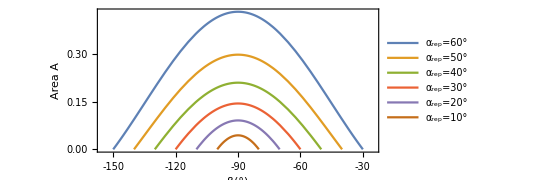

```mathematica
aDeg = {60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*1/8 l^2 (-Cos[2 a]+Cos[2 θD π/180]) Csc[a] Sec[a], {a,as}]],
{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},
Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Right,Top}],FrameLabel->{"β(°)","Area A"},AspectRatio->.45]
```

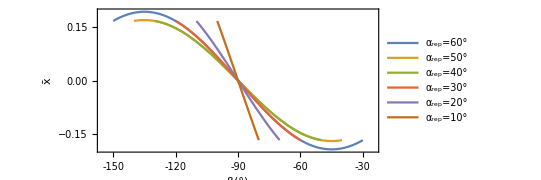

```mathematica
aDeg = {60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*-1/6 l Cos[θD π/180] Csc[a] Sec[a] Sin[θD π/180], {a,as}]],
{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},
Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Right,Top}],FrameLabel->{"β(°)","x̄"},AspectRatio->.45]
```

```mathematica
Manipulate[
aDeg = {15,30,av,45,60};
as =aDeg π/180;
Plot[Evaluate[Table[ If[Abs[θD π/180]>a,ⅈ,1]*-1/6 l Cos[θD π/180] Csc[a] Sec[a] Sin[θD π/180], {a,as}]],{θD,-90,90},
Ticks->{{-60,-45,-30,-15,15,30,45,60},Automatic},PlotRange-> {{-70,70},All},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Left,Bottom}],AxesLabel->{"θ (°)","X mean"}]
,{av,5,75}]
```

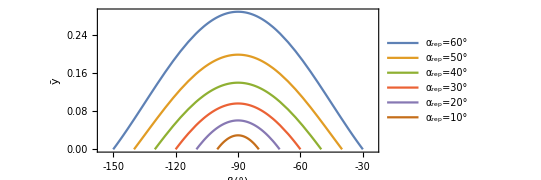

```mathematica
aDeg ={60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*1/12 l (-Cos[2 a]+Cos[2 θD π/180]) Csc[a] Sec[a], {a,as}]],
{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},
Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Right,Top}],FrameLabel->{"β(°)","
ȳ"},AspectRatio->.45]
```

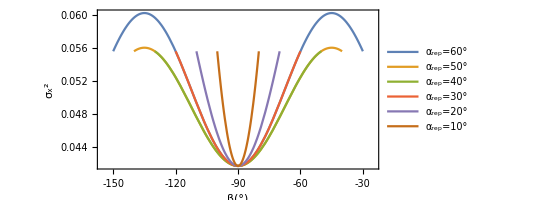

```mathematica
aDeg = {60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*-1/576 l^2 (-4+3 Cos[4 a]+Cos[4 θD π/180]) Csc[a]^2 Sec[a]^2, {a,as}]],
{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},
Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Right,Bottom}],FrameLabel->{"β(°)","σ_x^2"},AspectRatio->1/2]
```

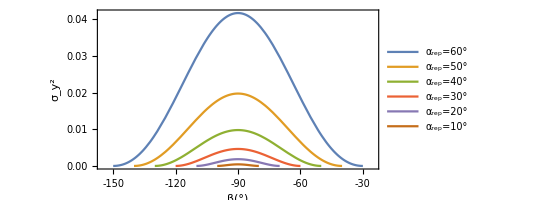

```mathematica
aDeg = {60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*1/72 l^2 (Cot[2 a]-Cos[2 θD π/180] Csc[2a])^2, {a,as}]],
{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},

Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Right,Top}],FrameLabel->{"β(°)","σ_y^2"},AspectRatio->1/2]
```

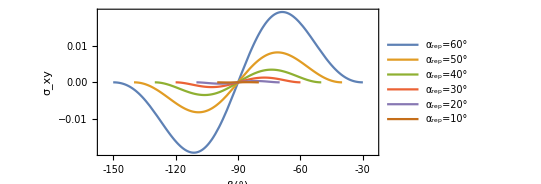

```mathematica
aDeg = {60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*1/72 l^2 (Cot[2 a]-Cos[2 θD π/180] Csc[2a])^2 Sin[2 θD π/180], {a,as}]],
{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},

Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Right,Bottom}],FrameLabel->{"β(°)","σ_xy"},AspectRatio->.46]
```

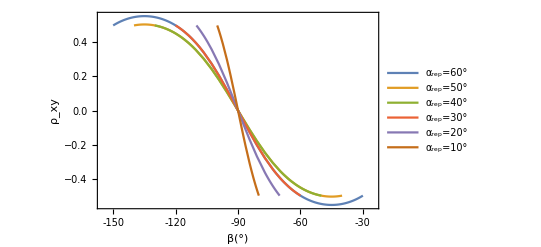

```mathematica
aDeg = {60,50,40,30,20,10};
as =aDeg π/180;
Plot[Evaluate[Table[θD=βD +90; If[Abs[θD π/180]>a,ⅈ,1]*
(4 √2  (Cos[2 a]-Cos[2 θD π/180]) Csc[2 a]^2 Sin[2 θD π/180])/(√(- (Cos[2 a]-Cos[2 θD π/180])^2 (-4+3 Cos[4 a]+Cos[4 θD π/180]) Csc[a]^4 Sec[a]^4))
, {a,as}]],{βD ,-180,0},
FrameTicks->{{-150,-135,-120,-105,-90,-75,-60,-45,-30,-15},Automatic},PlotRange-> {{-155,-25},All},

Frame->{True,True,False, False},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Left,Bottom}],FrameLabel->{"β(°)","ρ_xy"}]
```

```mathematica
θD=βD +90;
```